## Extra bits

L = 3

nParticles = 2

Extra bits for moves: 1

J Matrix:

(0 | J01 | J02
J01 | 0 | J12
J02 | J12 | 0)

Total configurations: 6

First few: {{1,2,0},{2,1,0},{1,0,2},{2,0,1},{0,1,2}}

Transition matrix row sums: {1,1,1,1,1,1}

Transition matrix:

(0 | 1/2 | 1/4 | 0 | 0 | 1/4
1/2 | 0 | 0 | 1/4 | 1/4 | 0
1/4 | 0 | 0 | 1/4 | 1/2 | 0
0 | 1/4 | 1/4 | 0 | 0 | 1/2
0 | 1/4 | 1/2 | 0 | 0 | 1/4
1/4 | 0 | 0 | 1/2 | 1/4 | 0)

Computing detailed balance violations...

Non-literal-zero violations: 0

Unique violations to simplify: 0 (reduced from 0)

Detailed balance: SATISFIED (all violations are literal zeros)

Decision tree for first state:

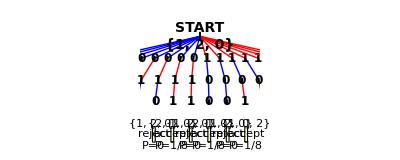

Decision tree for second state:

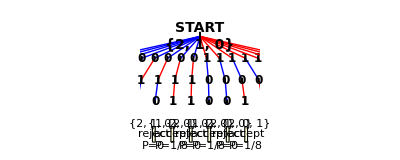

```mathematica
ClearAll["Global`*"]

(* =========================================*)
(*SETUP*)
(* =========================================*)

L=3;
nParticles=2;
β=Symbol["β"];

(*SPECIFY NUMBER OF BITS FOR THE MOVE*)
nExtraBits=1;  (*0=standard Kawasaki,1=reversal/translation,etc.*)

Print["L = ",L];
Print["nParticles = ",nParticles];
Print["Extra bits for moves: ",nExtraBits];

(* =========================================*)
(*SYMBOLIC J MATRIX*)
(* =========================================*)

GenerateSymbolicJ[n_]:=Module[{J=Table[0,{n+1},{n+1}]},Do[If[i<j,J[[i+1,j+1]]=Symbol["J"<>ToString[i]<>ToString[j]];
J[[j+1,i+1]]=J[[i+1,j+1]]],{i,0,n},{j,0,n}];
J]

JMatrix=GenerateSymbolicJ[nParticles];

Print["J Matrix:"];
Print[JMatrix//MatrixForm];

(* =========================================*)
(*ENERGY*)
(* =========================================*)

SymbolicEnergy[lattice_]:=Module[{E=0,i,j},Do[j=If[i==Length[lattice],1,i+1];
If[lattice[[i]]!=0&&lattice[[j]]!=0,E-=JMatrix[[lattice[[i]]+1,lattice[[j]]+1]]],{i,Length[lattice]}];
E]

(* =========================================*)
(*CONFIGURATIONS*)
(* =========================================*)

GenerateAllConfigs[L_,n_]:=Flatten[Table[Module[{lat=ConstantArray[0,L]},Do[lat[[pos[[i]]]]=perm[[i]],{i,n}];
lat],{pos,Subsets[Range[L],{n}]},{perm,Permutations[Range[n]]}],1]

states=GenerateAllConfigs[L,nParticles];
Print["Total configurations: ",Length[states]];
Print["First few: ",Take[states,Min[5,Length[states]]]];

(* =========================================*)
(*TREE RANDOMNESS*)
(* =========================================*)

$BinaryChoices={};
$BinaryIndex=1;

BinaryBit[]:=Module[{b},b=$BinaryChoices[[$BinaryIndex]];
$BinaryIndex++;
b]

DecodeInteger[nBits_]:=FromDigits[Table[BinaryBit[],{nBits}],2]

(* =========================================*)
(*KAWASAKI MOVE-normalized probabilities*)
(* =========================================*)

KawasakiMoveFromBitsold[lattice_]:=Module[{Lsize,nBits,raw,i,j,new,ΔE,p,siteProb},Lsize=Length[lattice];
nBits=Ceiling[Log2[Lsize]];
(*Consume extra bits if specified*)If[nExtraBits>0,DecodeInteger[nExtraBits]];
siteProb=1/(2^(nBits+nExtraBits));
raw=DecodeInteger[nBits];
i=1+Mod[raw,Lsize];
j=If[i==Lsize,1,i+1];
If[lattice[[i]]==lattice[[j]],Return[{"no-swap",lattice,siteProb}]];
new=lattice;
new[[{i,j}]]=lattice[[{j,i}]];
ΔE=SymbolicEnergy[new]-SymbolicEnergy[lattice];
p=Piecewise[{{1,ΔE<=0},{Exp[-β ΔE],ΔE>0}}];
{{"accept",new,siteProb*p},{"reject",lattice,siteProb*(1-p)}}]


KawasakiMoveFromBits[lattice_]:=Module[{Lsize,nBits,raw,i,j,new,ΔE,p,siteProb},Lsize=Length[lattice];
nBits=Ceiling[Log2[Lsize]];
(*Consume extra bits if specified*)If[nExtraBits>0,DecodeInteger[nExtraBits]];
siteProb=1/(2^(nBits+nExtraBits));
raw=DecodeInteger[nBits];
i=1+Mod[raw,Lsize];
j=If[i==Lsize,1,i+1];
If[lattice[[i]]==lattice[[j]],Return[{"no-swap",lattice,siteProb}]];
new=lattice;
new[[{i,j}]]=lattice[[{j,i}]];
ΔE=SymbolicEnergy[new]-SymbolicEnergy[lattice];
p=Piecewise[{{1,ΔE<=0},{Exp[-β ΔE],ΔE>0}}];
{{"accept",new,siteProb*p},{"reject",lattice,siteProb*(1-p)}}]





(* =========================================*)
(*TREE ENUMERATION*)
(* =========================================*)

EnumerateTree[lattice_]:=Module[{nBitsForSite,nBitsTotal,allBits,results},nBitsForSite=Ceiling[Log2[Length[lattice]]];
nBitsTotal=nBitsForSite+nExtraBits;
allBits=Tuples[{0,1},nBitsTotal];
results=Flatten[Table[($BinaryChoices=bits;
$BinaryIndex=1;
With[{out=KawasakiMoveFromBits[lattice]},If[First[out]==="no-swap",{{bits,"no-swap",out[[2]],out[[3]]}},{{bits,"accept",out[[1,2]],out[[1,3]]},{bits,"reject",out[[2,2]],out[[2,3]]}}]]),{bits,allBits}],1];
results]

(* =========================================*)
(*TREE VISUALIZATION*)
(* =========================================*)

VisualizeDecisionTree[initialState_]:=Module[{tree,nBitsForSite,nBitsTotal,yLevels,xSpacing,nodeRadius,rootX,rootY,pathGraphics,baseXPositions,imageWidth,plotRangeX,Lsize,rootGraphics},tree=EnumerateTree[initialState];
Lsize=Length[initialState];
nBitsForSite=Ceiling[Log2[Lsize]];
nBitsTotal=nBitsForSite+nExtraBits;
imageWidth=Max[1800,Length[tree]*60];
plotRangeX=Max[50,Length[tree]*3];
yLevels=Range[nBitsTotal,0,-1]*2;
xSpacing=Max[20,Length[tree]*1.5];
nodeRadius=0.2;
rootX=0;
rootY=yLevels[[1]];
baseXPositions=Table[(i-(Length[tree]+1)/2)*(xSpacing/1.5),{i,Length[tree]}];
pathGraphics=Table[Module[{path,pathType,finalState,probability,currentX,currentY,lineGraphics,circleGraphics,labelGraphics,bit,level,nextX,nextY,edgeColor,leafY,leafX,leafColor,leafText,treeEntry},treeEntry=tree[[i]];
path=Part[treeEntry,1];
pathType=Part[treeEntry,2];
finalState=Part[treeEntry,3];
probability=Part[treeEntry,4];
currentX=rootX;
currentY=rootY;
lineGraphics={};
circleGraphics={};
labelGraphics={};
Do[bit=path[[level]];
nextX=baseXPositions[[i]]+(currentX-baseXPositions[[i]])*0.3;
nextY=yLevels[[level+1]];
edgeColor=Which[bit==0,Blue,bit==1,Red,True,Black];
AppendTo[lineGraphics,{edgeColor,Thickness[0.0025],Arrowheads[0],Arrow[{{currentX,currentY},{nextX,nextY}}]}];
AppendTo[circleGraphics,{White,EdgeForm[{Black,Thin}],Disk[{nextX,nextY},nodeRadius]}];
AppendTo[labelGraphics,Text[Style[bit,Bold,12],{nextX,nextY}]];
currentX=nextX;
currentY=nextY;,{level,Length[path]}];
leafY=-3;
leafX=baseXPositions[[i]];
{leafColor,leafText}=Which[pathType=="no-swap",{LightGray,Column[{Style[ToString[finalState],Gray,12],Style["no-swap",Gray,10]},Center,Spacings->0.1]},pathType=="accept",{LightYellow,Column[{Style[ToString[finalState],Black,Bold,12],Style["accept",Black,10],Style["P="<>ToString[TraditionalForm[Simplify[probability]]],Black,10]},Center,Spacings->0.1]},pathType=="reject",{LightYellow,Column[{Style[ToString[finalState],Black,Bold,12],Style["reject",Black,10],Style["P="<>ToString[TraditionalForm[Simplify[probability]]],Black,10]},Center,Spacings->0.1]}];
AppendTo[circleGraphics,{leafColor,EdgeForm[{Black,Thin}],Rectangle[{leafX-1.2,leafY-0.7},{leafX+1.2,leafY+0.7}]}];
AppendTo[labelGraphics,Text[leafText,{leafX,leafY}]];
{lineGraphics,circleGraphics,labelGraphics}],{i,Length[tree]}];
rootGraphics={{LightBlue,EdgeForm[{Black,Thick}],Disk[{rootX,rootY},nodeRadius*2]},Text[Style["START\n"<>ToString[initialState],Bold,14],{rootX,rootY}]};
Pane[Graphics[{pathGraphics,rootGraphics},PlotRange->{{-plotRangeX,plotRangeX},{-4,yLevels[[1]]+2}},AspectRatio->0.4,Background->White],{1800,600},Scrollbars->True]]

(* =========================================*)
(*TRANSITION MATRIX*)
(* =========================================*)

EnumerateTransitions[lattice_]:=Module[{tree},tree=EnumerateTree[lattice];
Merge[Table[{lattice,tree[[i,3]]}->tree[[i,4]],{i,Length[tree]}],Total]]

BuildTransitionMatrix[states_]:=Module[{n,idx,M,trans},n=Length[states];
idx=AssociationThread[states->Range[n]];
M=ConstantArray[0,{n,n}];
Do[trans=EnumerateTransitions[s];
KeyValueMap[(M[[idx[#1[[1]]],idx[#1[[2]]]]]=#2)&,trans],{s,states}];
M]

transitionMatrix=BuildTransitionMatrix[states];

Print["\nTransition matrix row sums: ",Simplify[Total[transitionMatrix,{2}]]];
Print["Transition matrix:"];
If[Length[states]<=20,Print[transitionMatrix//MatrixForm],Print["Showing 5x5 block:"];
Print[Take[transitionMatrix,{1,5},{1,5}]//MatrixForm]];

(* =========================================*)
(*DETAILED BALANCE CHECK-OPTIMIZED*)
(* =========================================*)

boltzmannWeights=Table[Exp[-β*SymbolicEnergy[states[[i]]]],{i,Length[states]}];

Print["Computing detailed balance violations..."];

violations=Flatten[Table[boltzmannWeights[[i]]*transitionMatrix[[i,j]]-boltzmannWeights[[j]]*transitionMatrix[[j,i]],{i,Length[states]},{j,i+1,Length[states]}]];

nonZero=DeleteCases[violations,0];

Print["Non-literal-zero violations: ",Length[nonZero]];

uniqueViolations=DeleteDuplicates[nonZero];

Print["Unique violations to simplify: ",Length[uniqueViolations]," (reduced from ",Length[nonZero],")"];

If[Length[uniqueViolations]>0,Print["Applying FullSimplify to unique violations..."];
simplifiedUnique=ParallelMap[FullSimplify,uniqueViolations];
remainingViolations=Select[simplifiedUnique,#=!=0&];
Print["\nDetailed balance: ",If[Length[remainingViolations]==0,"SATISFIED (all unique violations symbolically reduced to 0)",ToString[Length[remainingViolations]]<>" unique violations remain after FullSimplify"]];
If[Length[remainingViolations]>0&&Length[remainingViolations]<=3,Print["Remaining violations: "];
Do[Print[remainingViolations[[i]]],{i,Length[remainingViolations]}]];,Print["\nDetailed balance: SATISFIED (all violations are literal zeros)"];];

(* =========================================*)
(*VISUALIZE TREES FOR FIRST TWO STATES*)
(* =========================================*)

Print["\nDecision tree for first state:"];
tree1=VisualizeDecisionTree[states[[1]]];
Print[tree1];

If[Length[states]>1,Print["\nDecision tree for second state:"];
tree2=VisualizeDecisionTree[states[[2]]];
Print[tree2];];
```

Note: To get this to work - need to be able to provide more complex

L = 4

nParticles = 2

Extra bits for moves: 1

J Matrix:

(0 | J01 | J02
J01 | 0 | J12
J02 | J12 | 0)

Total configurations: 12

First few: {{1,2,0,0},{2,1,0,0},{1,0,2,0},{2,0,1,0},{1,0,0,2}}

Transition matrix row sums: {1,1,1,1,1,1,1,1,1,1,1,1}

Transition matrix:

(1/4+1/2 (1-(Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}])) | 1/4 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0
1/4 | 1/4+1/2 (1-(Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}])) | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0 | 0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0 | 0
1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1-(Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 0 | 0 | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}])
0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1-(Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0
0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 1/4+1/2 (1-(Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}])) | 1/4 | 0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0 | 0
0 | 0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 1/4 | 1/4+1/2 (1-(Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}])) | 0 | 0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0
0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0 | 0 | 1/4+1/2 (1-(Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}])) | 1/4 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0 | 0
0 | 0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0 | 1/4 | 1/4+1/2 (1-(Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}])) | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0
0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1-(Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0
1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 0 | 0 | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1-(Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}]) | 0 | 1/4 (Piecewise[{{1, -J12≤0}, {ⅇ^(J12 β), -J12>0}, {0, True}}])
0 | 0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0 | 0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 1/4+1/2 (1-(Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}])) | 1/4
0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 0 | 0 | 0 | 0 | 0 | 0 | 1/4 (Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}]) | 1/4 | 1/4+1/2 (1-(Piecewise[{{1, J12≤0}, {ⅇ^(-J12 β), J12>0}, {0, True}}])))

Computing detailed balance violations...

Non-literal-zero violations: 16

Unique violations to simplify: 2 (reduced from 16)

Applying FullSimplify to unique violations...

Detailed balance: SATISFIED (all unique violations symbolically reduced to 0)

Decision tree for first state:

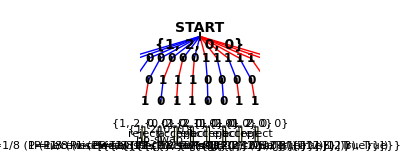

Decision tree for second state:

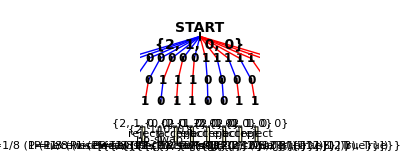

```mathematica
ClearAll["Global`*"]

(* =========================================*)
(*SETUP*)
(* =========================================*)

L=4;
nParticles=2;
β=Symbol["β"];

(*SPECIFY NUMBER OF BITS FOR THE MOVE*)
nExtraBits=1;  (*1 for symmetric translation*)

Print["L = ",L];
Print["nParticles = ",nParticles];
Print["Extra bits for moves: ",nExtraBits];

(* =========================================*)
(*SYMBOLIC J MATRIX*)
(* =========================================*)

GenerateSymbolicJ[n_]:=Module[{J=Table[0,{n+1},{n+1}]},Do[If[i<j,J[[i+1,j+1]]=Symbol["J"<>ToString[i]<>ToString[j]];
J[[j+1,i+1]]=J[[i+1,j+1]]],{i,0,n},{j,0,n}];
J]

JMatrix=GenerateSymbolicJ[nParticles];

Print["J Matrix:"];
Print[JMatrix//MatrixForm];

(* =========================================*)
(*ENERGY*)
(* =========================================*)

SymbolicEnergy[lattice_]:=Module[{E=0,i,j},Do[j=If[i==Length[lattice],1,i+1];
If[lattice[[i]]!=0&&lattice[[j]]!=0,E-=JMatrix[[lattice[[i]]+1,lattice[[j]]+1]]],{i,Length[lattice]}];
E]

(* =========================================*)
(*CONFIGURATIONS*)
(* =========================================*)

GenerateAllConfigs[L_,n_]:=Flatten[Table[Module[{lat=ConstantArray[0,L]},Do[lat[[pos[[i]]]]=perm[[i]],{i,n}];
lat],{pos,Subsets[Range[L],{n}]},{perm,Permutations[Range[n]]}],1]

states=GenerateAllConfigs[L,nParticles];
Print["Total configurations: ",Length[states]];
Print["First few: ",Take[states,Min[5,Length[states]]]];

(* =========================================*)
(*TREE RANDOMNESS*)
(* =========================================*)

$BinaryChoices={};
$BinaryIndex=1;

BinaryBit[]:=Module[{b},b=$BinaryChoices[[$BinaryIndex]];
$BinaryIndex++;
b]

DecodeInteger[nBits_]:=FromDigits[Table[BinaryBit[],{nBits}],2]

KawasakiMoveFromBitsWithSymmetricTranslation[lattice_]:=Module[{Lsize,nBits,raw,i,j,new,ΔE,p,siteProb,kawasakiNew,translatedNew,translationBit,translateRight,segments,seg,foundSegment,pos},Lsize=Length[lattice];
nBits=Ceiling[Log2[Lsize]];
(*Read one bit for translation direction*)translationBit=BinaryBit[];
translateRight=(translationBit==1);
siteProb=1/(2^(nBits+1));
raw=DecodeInteger[nBits];
i=1+Mod[raw,Lsize];
j=If[i==Lsize,1,i+1];
(*STEP 1:Standard Kawasaki move*)If[lattice[[i]]==lattice[[j]],Return[{"no-swap",lattice,siteProb}]];
kawasakiNew=lattice;
kawasakiNew[[{i,j}]]=lattice[[{j,i}]];
ΔE=SymbolicEnergy[kawasakiNew]-SymbolicEnergy[lattice];
p=Piecewise[{{1,ΔE<=0},{Exp[-β ΔE],ΔE>0}}];
(*Return result*){{"accept",kawasakiNew,siteProb*p},{"reject",lattice,siteProb*(1-p)}}]

(* =========================================*)
(*TREE ENUMERATION*)
(* =========================================*)

EnumerateTree[lattice_]:=Module[{nBitsForSite,nBitsTotal,allBits,results},nBitsForSite=Ceiling[Log2[Length[lattice]]];
nBitsTotal=nBitsForSite+nExtraBits;
allBits=Tuples[{0,1},nBitsTotal];
results=Flatten[Table[($BinaryChoices=bits;
$BinaryIndex=1;
With[{out=KawasakiMoveFromBitsWithSymmetricTranslation[lattice]},If[First[out]==="no-swap",{{bits,"no-swap",out[[2]],out[[3]]}},{{bits,"accept",out[[1,2]],out[[1,3]]},{bits,"reject",out[[2,2]],out[[2,3]]}}]]),{bits,allBits}],1];
results]

(* =========================================*)
(*TREE VISUALIZATION*)
(* =========================================*)

VisualizeDecisionTree[initialState_]:=Module[{tree,nBitsForSite,nBitsTotal,yLevels,xSpacing,nodeRadius,rootX,rootY,pathGraphics,baseXPositions,imageWidth,plotRangeX,Lsize,rootGraphics},tree=EnumerateTree[initialState];
Lsize=Length[initialState];
nBitsForSite=Ceiling[Log2[Lsize]];
nBitsTotal=nBitsForSite+nExtraBits;
imageWidth=Max[1800,Length[tree]*60];
plotRangeX=Max[50,Length[tree]*3];
yLevels=Range[nBitsTotal,0,-1]*2;
xSpacing=Max[20,Length[tree]*1.5];
nodeRadius=0.2;
rootX=0;
rootY=yLevels[[1]];
baseXPositions=Table[(i-(Length[tree]+1)/2)*(xSpacing/1.5),{i,Length[tree]}];
pathGraphics=Table[Module[{path,pathType,finalState,probability,currentX,currentY,lineGraphics,circleGraphics,labelGraphics,bit,level,nextX,nextY,edgeColor,leafY,leafX,leafColor,leafText,treeEntry},treeEntry=tree[[i]];
path=Part[treeEntry,1];
pathType=Part[treeEntry,2];
finalState=Part[treeEntry,3];
probability=Part[treeEntry,4];
currentX=rootX;
currentY=rootY;
lineGraphics={};
circleGraphics={};
labelGraphics={};
Do[bit=path[[level]];
nextX=baseXPositions[[i]]+(currentX-baseXPositions[[i]])*0.3;
nextY=yLevels[[level+1]];
edgeColor=Which[bit==0,Blue,bit==1,Red,True,Black];
AppendTo[lineGraphics,{edgeColor,Thickness[0.0025],Arrowheads[0],Arrow[{{currentX,currentY},{nextX,nextY}}]}];
AppendTo[circleGraphics,{White,EdgeForm[{Black,Thin}],Disk[{nextX,nextY},nodeRadius]}];
AppendTo[labelGraphics,Text[Style[bit,Bold,12],{nextX,nextY}]];
currentX=nextX;
currentY=nextY;,{level,Length[path]}];
leafY=-3;
leafX=baseXPositions[[i]];
{leafColor,leafText}=Which[pathType=="no-swap",{LightGray,Column[{Style[ToString[finalState],Gray,12],Style["no-swap",Gray,10]},Center,Spacings->0.1]},pathType=="accept",{LightYellow,Column[{Style[ToString[finalState],Black,Bold,12],Style["accept",Black,10],Style["P="<>ToString[TraditionalForm[Simplify[probability]]],Black,10]},Center,Spacings->0.1]},pathType=="reject",{LightYellow,Column[{Style[ToString[finalState],Black,Bold,12],Style["reject",Black,10],Style["P="<>ToString[TraditionalForm[Simplify[probability]]],Black,10]},Center,Spacings->0.1]}];
AppendTo[circleGraphics,{leafColor,EdgeForm[{Black,Thin}],Rectangle[{leafX-1.2,leafY-0.7},{leafX+1.2,leafY+0.7}]}];
AppendTo[labelGraphics,Text[leafText,{leafX,leafY}]];
{lineGraphics,circleGraphics,labelGraphics}],{i,Length[tree]}];
rootGraphics={{LightBlue,EdgeForm[{Black,Thick}],Disk[{rootX,rootY},nodeRadius*2]},Text[Style["START\n"<>ToString[initialState],Bold,14],{rootX,rootY}]};
Pane[Graphics[{pathGraphics,rootGraphics},PlotRange->{{-plotRangeX,plotRangeX},{-4,yLevels[[1]]+2}},AspectRatio->0.4,Background->White],{1800,600},Scrollbars->True]]

(* =========================================*)
(*TRANSITION MATRIX*)
(* =========================================*)

EnumerateTransitions[lattice_]:=Module[{tree},tree=EnumerateTree[lattice];
Merge[Table[{lattice,tree[[i,3]]}->tree[[i,4]],{i,Length[tree]}],Total]]

BuildTransitionMatrix[states_]:=Module[{n,idx,M,trans},n=Length[states];
idx=AssociationThread[states->Range[n]];
M=ConstantArray[0,{n,n}];
Do[trans=EnumerateTransitions[s];
KeyValueMap[(M[[idx[#1[[1]]],idx[#1[[2]]]]]=#2)&,trans],{s,states}];
M]

transitionMatrix=BuildTransitionMatrix[states];

Print["\nTransition matrix row sums: ",Simplify[Total[transitionMatrix,{2}]]];
Print["Transition matrix:"];
If[Length[states]<=20,Print[transitionMatrix//MatrixForm],Print["Showing 5x5 block:"];
Print[Take[transitionMatrix,{1,5},{1,5}]//MatrixForm]];

(* =========================================*)
(*DETAILED BALANCE CHECK-OPTIMIZED*)
(* =========================================*)

boltzmannWeights=Table[Exp[-β*SymbolicEnergy[states[[i]]]],{i,Length[states]}];

Print["Computing detailed balance violations..."];

violations=Flatten[Table[boltzmannWeights[[i]]*transitionMatrix[[i,j]]-boltzmannWeights[[j]]*transitionMatrix[[j,i]],{i,Length[states]},{j,i+1,Length[states]}]];

nonZero=DeleteCases[violations,0];

Print["Non-literal-zero violations: ",Length[nonZero]];

uniqueViolations=DeleteDuplicates[nonZero];

Print["Unique violations to simplify: ",Length[uniqueViolations]," (reduced from ",Length[nonZero],")"];

If[Length[uniqueViolations]>0,Print["Applying FullSimplify to unique violations..."];
simplifiedUnique=ParallelMap[FullSimplify,uniqueViolations];
remainingViolations=Select[simplifiedUnique,#=!=0&];
Print["\nDetailed balance: ",If[Length[remainingViolations]==0,"SATISFIED (all unique violations symbolically reduced to 0)",ToString[Length[remainingViolations]]<>" unique violations remain after FullSimplify"]];
If[Length[remainingViolations]>0&&Length[remainingViolations]<=30,Print["Remaining violations: "];
Do[Print[remainingViolations[[i]]],{i,Length[remainingViolations]}]];,Print["\nDetailed balance: SATISFIED (all violations are literal zeros)"];];

(* =========================================*)
(*VISUALIZE TREES FOR FIRST TWO STATES*)
(* =========================================*)

Print["\nDecision tree for first state:"];
tree1=VisualizeDecisionTree[states[[1]]];
Print[tree1];

If[Length[states]>1,Print["\nDecision tree for second state:"];
tree2=VisualizeDecisionTree[states[[2]]];
Print[tree2];];
```